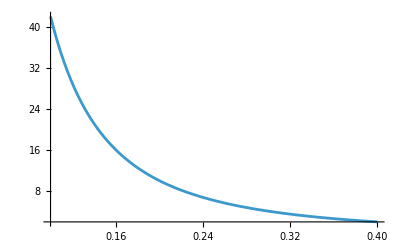

```mathematica
ClearAll[A4,M4,M4ds,residueExpr,g2Expr,g3Expr,ratioExpr,ratio,μ,τ,σ];

(*5d amplitude*)
A4[s_,t_]:=Module[{u=-s-t},(s^2+t^2+u^2)^2*Gamma[-s/4] Gamma[-t/4] Gamma[-u/4]/(Gamma[1+s/4] Gamma[1+t/4] Gamma[1+u/4])];

(*4d symmetric amplitude with explicit KK mass parameter μ*)
M4[s_,t_,μ_]:=Module[{u=4 μ^2-s-t},A4[s+4 μ^2,t]+A4[s,t+4 μ^2]+(s^2+t^2+u^2)^2*Gamma[-s/4] Gamma[-t/4] Gamma[-u/4]/(Gamma[1+s/4] Gamma[1+t/4] Gamma[1+u/4])];

(*Differentiate once symbolically,then reuse*)
M4ds[s_,t_,μ_]:=D[M4[σ,t,μ],σ]/. σ->s;

(*Analytic residue formula*)
residueExpr[μ_,t_]:=((M4ds[2 μ^2,t,μ]*t)-M4[2 μ^2,t,μ]+M4[2 μ^2-t,t,μ])/t^2;

(*Compute the t-series once*)
g2Expr=SeriesCoefficient[residueExpr[μ,τ],{τ,0,0}];
g3Expr=SeriesCoefficient[residueExpr[μ,τ],{τ,0,1}];

(*Optional simplification once,not inside Plot*)
ratioExpr=Simplify[g3Expr/g2Expr,Assumptions->0<μ<2/5];

(*Numeric plotting function*)
ratio[m_?NumericQ]:=N[ratioExpr/. μ->m,30];

Plot[ratio[m],{m,1/10,4/10},PlotRange->All,WorkingPrecision->200,PlotPoints->25,MaxRecursion->2]
```